# HyperPlot: On the generation of temporally coherent hypergraphs

Hypergraphs are typically plotted in the Wolfram Language using WolframModelPlot and the Spring Electrical Embedding. However, when animating the expansion of  hypergraphs generated by the Wolfram Physics Project, graphs generated with this method do not use any information from previous graphs, and as such will often look vastly different from one updating event to the next. In this project, we implement a physics engine to continuously simulate the Spring Electrical Embedding of graphs as they expand in 2 and 3 dimensional spaces, guaranteeing temporal coherence between updating events. We also explore the conditions under which such graphs become infinitely dense within the space they occupy as well as applications of these graphs to other systems such as multiway tag systems.

## Packages & Functions

This project uses the SetReplace paclet to generate universes from the Wolfram Physics Project. The paclet returns data about each time state of the graphs which we will then animate with a physics simulation.

```mathematica
PacletInstall["SetReplace"]
Needs["SetReplace`"]
```

PacletObject[…]

WolframModel::shdw: Symbol WolframModel appears in multiple contexts {SetReplace`,Global`}; definitions in context SetReplace` may shadow or be shadowed by other definitions.

## Hypergraphs

### A brief overview of graphs

A graph consists of a set of vertices and the edges between them.

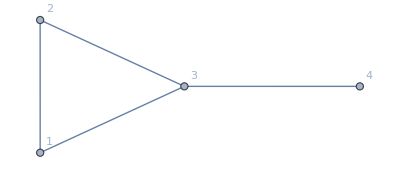

```mathematica
vertices  = {1,2,3,4};
edges = {1<->2,2<->3,3<->4,1<->3};
GraphPlot[Graph[vertices,edges],VertexLabels->All]
```

In this visual representation of a graph, edges are shown as lines between the two vertices they connect.  For this project, we will assume that graphs are multigraphs, meaning they can have multiple edges between two vertices or edges that go from a vertex to itself, as shown below:

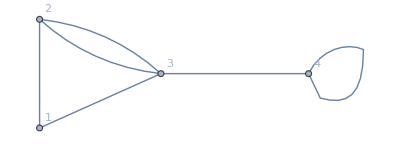

```mathematica
vertices  = {1,2,3,4};
edges = {1<->2,2<->3,2<->3,3<->4,1<->3,4<->4};
GraphPlot[Graph[vertices,edges],VertexLabels->All]
```

Graphs can be directed, meaning each edge only goes in one direction from a vertex  to another vertex .

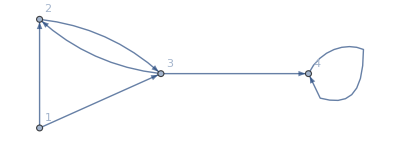

```mathematica
vertices  = {1,2,3,4};
edges = {1->2,2->3,3->2,3->4,1->3,4->4};
GraphPlot[Graph[vertices,edges],VertexLabels->All]
```

### Adjacency Matrices

The adjacency matrix of a graph is a square matrix of which the rows and columns are the vertices of the graph. The value of each cell  in the matrix is equal to the amount of edges going from  to .

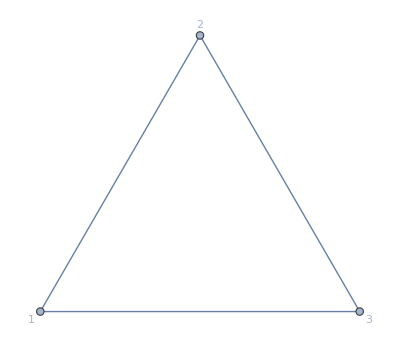
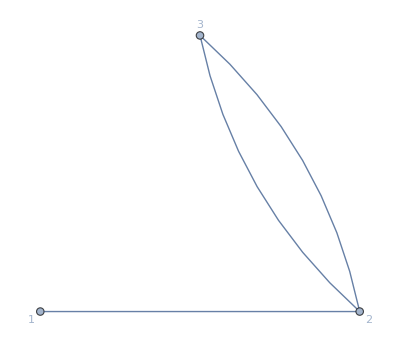
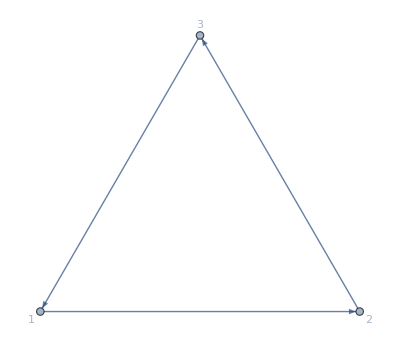
-Graphics- | -Graphics- | -Graphics-
(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0) | (0 | 1 | 0
1 | 0 | 2
0 | 2 | 0) | (0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)

```mathematica
graph1=Graph[{1<->2,2<->3,3<->1},GraphLayout->"CircularEmbedding",VertexLabels->All];
graph2=Graph[{1<->2,2<->3,2<->3},GraphLayout->"CircularEmbedding",VertexLabels->All];
graph3=Graph[{1->2,2->3,3->1},GraphLayout->"CircularEmbedding",VertexLabels->All];
matrix1 = MatrixForm[AdjacencyMatrix[graph1]];
matrix2 = MatrixForm[AdjacencyMatrix[graph2]];
matrix3 = MatrixForm[AdjacencyMatrix[graph3]];
Grid[{{graph1,graph2,graph3},{matrix1,matrix2,matrix3}}]
```

For undirected graphs, the adjacency matrices are symmetric, meaning if   is adjacent to , then   is also adjacent to .

### When Matrices become Tensors

A hypergraph is a generalization of a graph where edges can include any amount of vertices. This means that instead of representing an edge as  we can represent it as . Such a relation is called a hyperedge.
Hypergraphs have adjacency tensors instead of matrices, as their relations are of a higher arity.

```mathematica
MatrixForm[{{{1,2},{3,4}},{{5,6},{7,8}}}]
```

```mathematica
({{({{1}, {2}}), ({{3}, {4}})}, {({{5}, {6}}), ({{7}, {8}})}})
```

### Plotting hypergraphs

Just as regular edges can be represented by lines, hyperedges can be represented by polygons such that the vertices of the polygon are the vertices in the hyperedge.

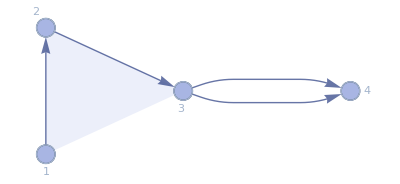

```mathematica
[{{1,2,3},{3,4},{3,4}},VertexLabels->All]
```

Here the shaded triangle represents the hyperedge .

## The Wolfram Physics Project

### Rules

In the Wolfram Physics Project, rules define how a physics model (graph) will grow with each update.

An example of a rule is {{x,y}→{{x,y},{y,z}}. This means that if the graph contains 2 vertices x and y which are connected, when the graph updates, there will be a connection between vertex y and a new vertex called z, as well as the previous connection.

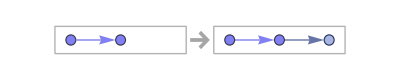

```mathematica
RulePlot[WolframModel[{{x,y}}->{{x,y},{y,z}}]]
```

Rules can also apply to hyperedges.

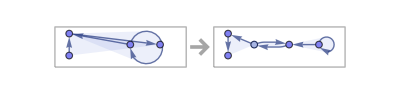

```mathematica
RulePlot[WolframModel[{{1,1,2},{3,2,4}}->{{4,4,1},{1,5,1},{5,2,3}}]]
```

### Repeated Rules

Rules have interesting emergent properties if we repeat them multiple times on a graph. “Repeating a rule” means that each iteration, all eligible groups of edges are updated using the rule.

Here is an example of one particular instance of applying a rule over and over again to a graph:

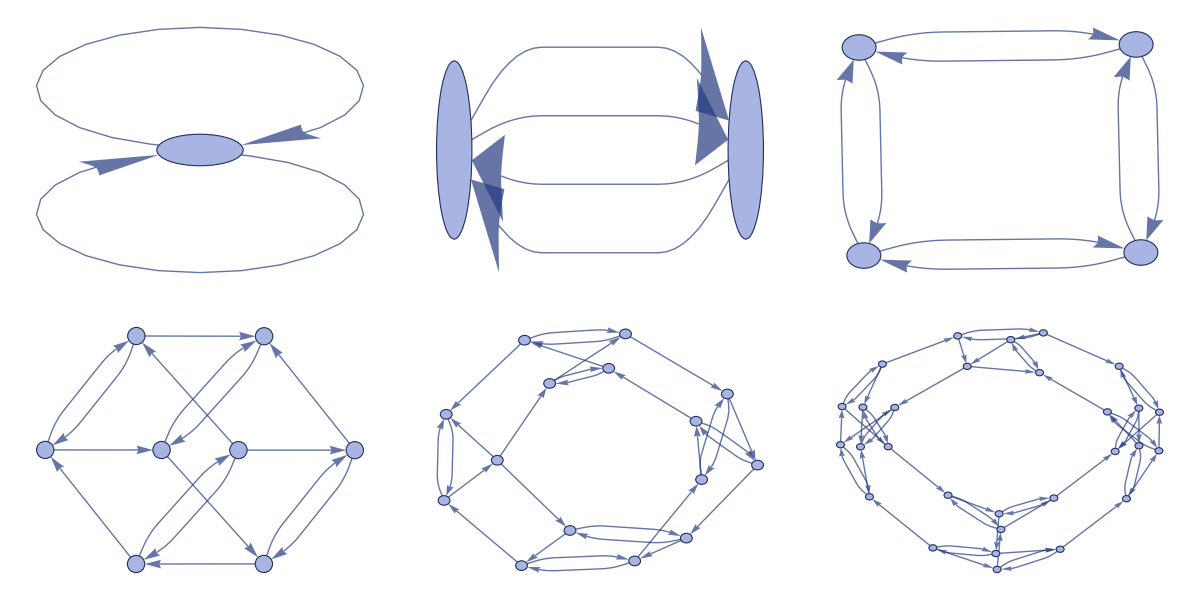

```mathematica
Grid[Partition[WolframModel[{{1,2},{1,3}}->{{4,1},{1,4},{4,2},{3,4}},{{1,1},{1,1}},5,"StatesPlotsList"],3]]
```

Rules can also use hyperedges.

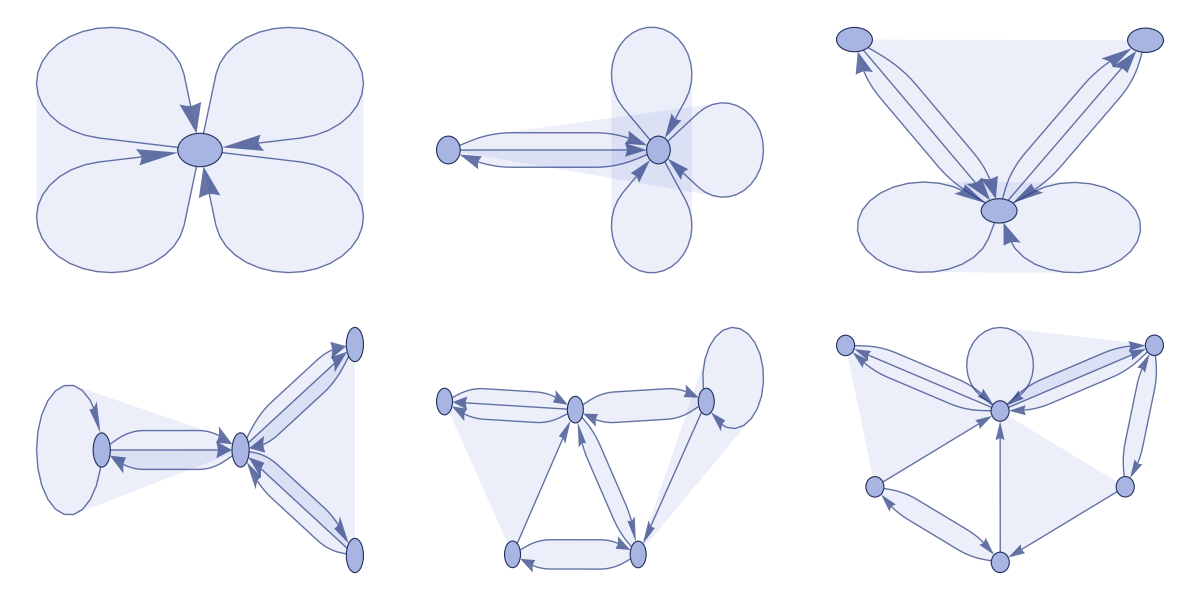

```mathematica
Grid[Partition[WolframModel[{{1,1,2},{3,2,4}}->{{4,4,1},{1,5,1},{5,2,3}},{{1,1,1},{1,1,1}},5,"StatesPlotsList"],3]]
```

## The Issue

Graphs (and hypergraphs) in the Wolfram Language are displayed using the “Spring Electrical Embedding” by default. This means that each vertex is treated like a point charge and each edge is treated as if it is a spring (in the case of hyperedges each vertex in the hyperedge exerts a spring force on each other vertex). Since the vertices naturally repel each other, the graph unfurls and becomes nicely spaced.

To watch a hypergraph expand as a rule is repeatedly applied to it, one can stitch together multiple plots of the hypergraph where each plot corresponds to the graph after each updating event. An updating event is when a rule is applied to one point, as opposed to an iteration when a rule is applied to every eligible point that was on the previous graph.

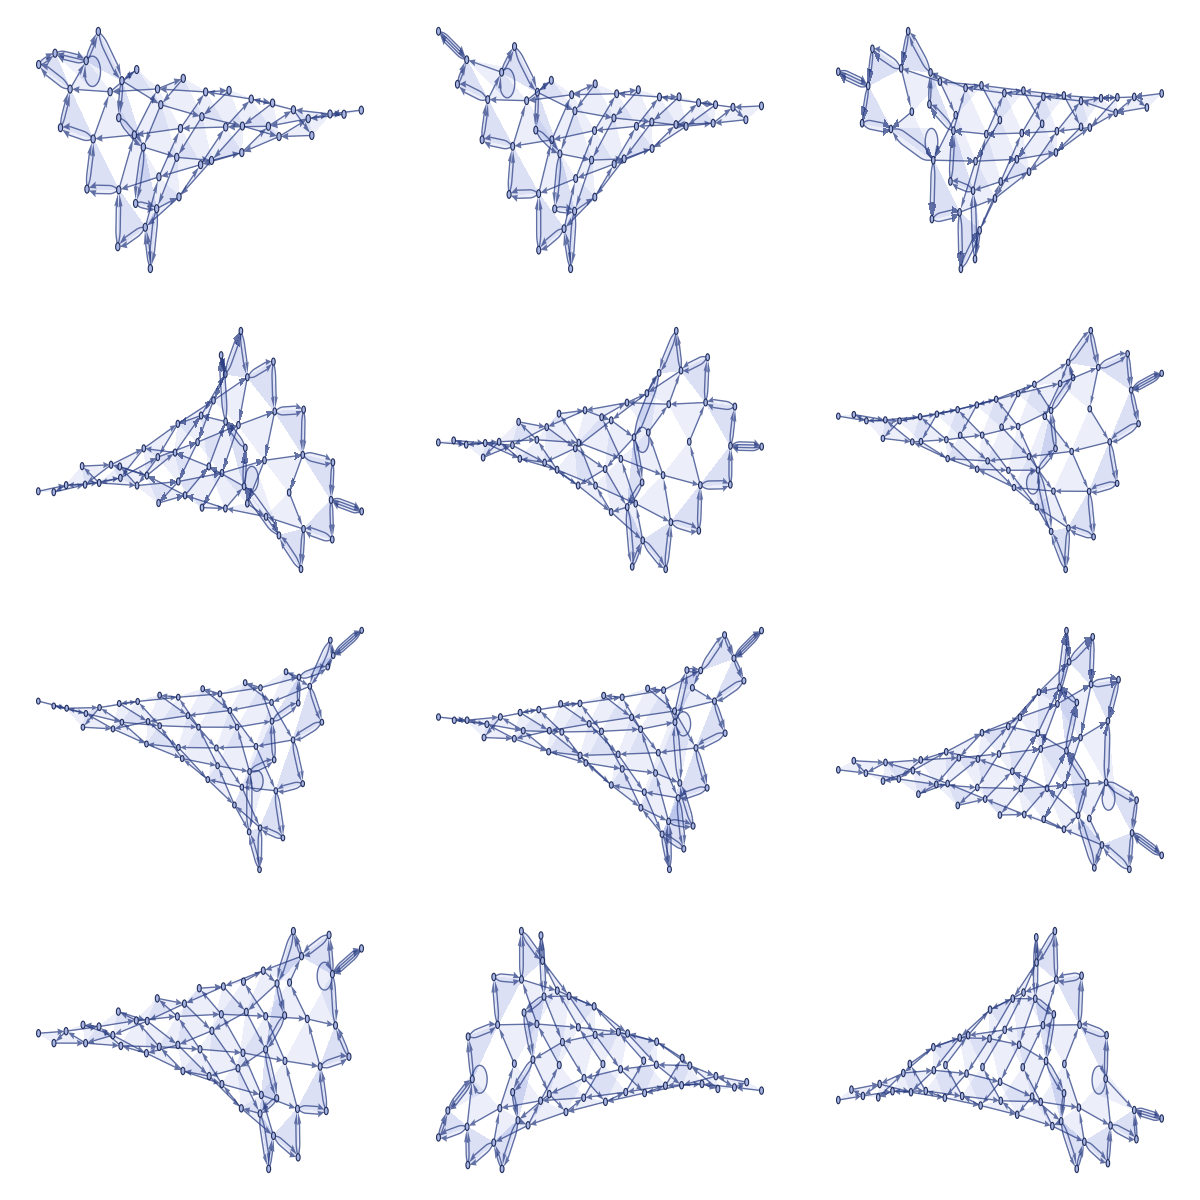

```mathematica
Grid[Partition[Take[WolframModel[{{1,1,2},{1,3,4}}->{{4,4,3},{2,5,3},{2,5,3}},{{1,1,1},{1,1,1}},55,"StatesPlotsList"],-12],3]]
```

The issue with stitching these plots together is that often they will completely flip or change orientation. In these 12 steps alone, the image flips 3 times. When animating an expanding graph, having the image completely change direction like this every so often would be disorienting.

One solution to this issue was presented in a previous project on the topic where each hypergraph (from each updating event) is stitched together into one large 4 dimensional hypergraph, only after which the spring electric simulation is run. While this does ensure that the graph will not significantly change frame to frame (as adjacent graphs have persistent vertices connected and therefore influence each others positions), the animation of the graph’s expansion is not smooth at all and the graph may still exhibit these unwanted behaviors longterm.

Another solution is to perform the physics simulation as the graph expands, not at each state. This way one can see the vertices move in real time, repelling each other with the spring electric system, allowing for the animation of the graph to not only be coherent long-term but also smooth short-term, as there is time for the graph to “interpolate” between updating events.

## Creating a Physics Engine

The Wolfram Language’s tools for visualizing graphs do not, unfortunately, allow us to watch the spring electric simulation at work. This means that we will need to replicate it with our own physics engine that does show each frame of the simulation.

### Electric Forces

In the simulation, each vertex exerts a repelling electric force on each other vertex.

```mathematica
getElectricForces[positions_]:=
Table[
Total[
Table[
If[j ==i,{0,0,0},potentialFunction[i,j]]
,{j,Nearest[positions, i, 10]}]
]
,{i, positions}]
```

The force’s strength is determined by the inverse square law, as defined by this function:

```mathematica
potentialFunction[pos1_,pos2_]:=First[MinimalBy[{Normalize[pos1-pos2]*potentialCap,electricConstant *Normalize[pos1-pos2]/SquaredEuclideanDistance[pos1,pos2]},Norm]]
```

The force is capped at a certain value to prevent errors in the simulation as well as dense packings of vertices from creating extremely high forces.

### Spring Forces

When two vertices are connected by an edge, they exert a spring force on each other. The spring force is modeled by a Hooke’s law spring, which means its force is proportional to the distance between the vertices.

```mathematica
getSpringForces[positions_,connections_]:=
Module[{vertexForceVectors,vertexIndexA,vertexIndexB, springForceAmount, springForceVector, vertexPositionA, vertexPositionB, distance, dimension},
dimension=Length[First[positions]];
vertexForceVectors=ConstantArray[0.,{Length[positions],dimension}];
Table[
Table[
vertexIndexA=First[interaction];
vertexIndexB=Last[interaction];
vertexPositionA=positions[[vertexIndexA]];
vertexPositionB=positions[[vertexIndexB]];
distance=Norm[vertexPositionA-vertexPositionB];
springForceAmount=Abs[distance-springRestoringDistance];
springForceVector=First[MinimalBy[{Normalize[vertexPositionA-vertexPositionB],Normalize[vertexPositionA-vertexPositionB]*springForceAmount},Norm]];
vertexForceVectors[[vertexIndexA]]-=springForceVector * springConstant;
vertexForceVectors[[vertexIndexB]]-=Minus[springForceVector] * springConstant;
,{interaction, getInteractions[connection]}]
,{connection, connections}];
vertexForceVectors
]
```

When hyperedges are involved, each hyperedge is broken down into “interactions”. These are subsets {v_i,v_j} of the set of points in the hyperedge e = {v_1,v_2, ... ,v_n} that contain 2 distinct elements v_i and v_j.

```mathematica
getInteractions[connection_]:=DeleteDuplicates[Select[Subsets[connection,2],MatchQ[{x_,y_}/;x!=y]]]
```

A spring force is then applied to the vertices in each interaction as if it was a regular edge.

Spring forces are also capped in the same way electric forces are to prevent excessively high force values.

### Damping

To prevent the simulation from continuing indefinitely, every frame velocities are damped by a set factor. This acts as a sort of “friction”.

```mathematica
applyDamping[velocities_]:=
Table[
(#*0.3)&/@v
,{v,velocities}]
```

### Updating Velocities & Positions

Once all forces have been calculated, they are ready to be applied to each point. This function adds the forces to the existing velocities.

```mathematica
updateVelocities[positions_,connections_,velocities_]:=
Module[{electricForces,springForces},
electricForces = getElectricForces[positions];
springForces= getSpringForces[positions,connections];
Table[
electricForces[[i]]+springForces[[i]]+velocities[[i]]
,{i, Length[velocities]}]
]
```

Velocities are then added to each point’s position. The “universalConstant” defines how quickly the points move, or essentially how large the step size is in the simulation.

```mathematica
updatePositions[positions_, velocities_]:=Table[positions[[i]] +universalConstant*velocities[[i]],{i, Length[positions]}]
```

Astute readers will point out that the electric and spring forces are actually accelerations since this simulation does not take into account mass. However “spring accelerations” doesn’t sound as nice as “spring forces” does, so I will not be changing the function names.

### Expanding the Graph

The physics system is complete, however this engine will only simulate a graph of constant size. If we want the graph to expand as the simulation progresses, there needs to be a function to add vertices & edges based on a Wolfram Model as the simulation progresses.

The first step in adding a vertex is to find which existing vertices it will share hyperedges with.

```mathematica
findVerticesConnectedTo[connections_,n_]:=
Flatten[
Table[
Cases[case,Except[n]]
,{case,Cases[connections,{___,n,___}]}]
]
```

Next, the vertex is placed near the average point of those it is connected to. A spherical shell is used to make sure that when the vertex is only connected to one other, they are not accidentally placed on top of each other. The spherical shell guarantees this minimum radius.

```mathematica
getNewVertexPosition[connections_,positions_,n_]:=
positionMean[
Table[positions[[i]]
,{i, findVerticesConnectedTo[connections,n]}]
]+RandomPoint[SphericalShell[{0,0,0},{0.4,0.5}]]
```

If the vertex is not connected to any other vertex through a hyperedge, it is placed at the center of the simulation by default.

```mathematica
positionMean[positions_]:=
If[Length[positions]==0,
{0,0,0},
Mean[positions]
]
```

This function applies this algorithm to every vertex that will be newly created in the next hypergraph update. It also gives all new vertices a starting velocity of zero.

```mathematica
addNewVertices[currentPositions_,velocities_,oldCons_,newCons_]:=
Module[{newPositions, newVelocities},
newPositions=currentPositions;
newVelocities=velocities;
Flatten[
Table[
If[point <= Length[currentPositions],Nothing,
AppendTo[newPositions,getNewVertexPosition[newCons,currentPositions,point]];
AppendTo[newVelocities,{0,0,0}];
]
,{point,DeleteDuplicates[Flatten[newCons]]}]
,1];
{newPositions,newVelocities}
]
```

### Putting it all Together

This function puts the entire physics simulation together.
It takes in a list of initial positions and velocities, the Wolfram Model to animate, and the amount of time steps to run it for.

```mathematica
iterate[positions_,velocities_,connections_,timesteps_]:=
Module[{posList, velList,newList},
posList = {};
velList={};
newList={};
posList=posList//Append[positions];
velList=velList//Append[velocities];
Table[
If[Divisible[step,graphUpdatePeriod],
newList=addNewVertices[posList[[step]],velList[[step]],connections[[Quotient[step,graphUpdatePeriod]]],connections[[Quotient[step,graphUpdatePeriod]+1]]];
posList = Append[posList,updatePositions[newList[[1]],newList[[2]]]];
velList = Append[velList,applyDamping[updateVelocities[newList[[1]], connections[[Quotient[step,graphUpdatePeriod]+1]],newList[[2]]]]];
,
posList = Append[posList,updatePositions[posList[[step]],velList[[step]]]];
velList = Append[velList,applyDamping[updateVelocities[posList[[step]], connections[[Quotient[step,graphUpdatePeriod]+1]],velList[[step]]]]];
];

,{step, timesteps}];
posList
]
```

The “graphUpdatePeriod” determines how many time steps there are between each hypergraph update event. Every time this number of time steps passes, new vertices are added to the graph using the process outlined before.

Positions & velocities are then updated using the physics simulation.

After computation is complete, the function outputs the complete list of all positions for each frame.

### Defining Constants

When coding a physics engine it is often useful to add constants that one can play around with later. These particular values work well for most 3 dimensional Wolfram Models tested during this project, however other values could work better in specific cases.

universalConstant: multiplier for velocities when they are applied - defines step size of graph
electricConstant: all electric forces are scaled by this amount
springConstant: all spring forces are scaled by this amount
springRestoringDistance: springs compressed past this distance will exert an outward force, and springs extended past it will exert an inward force.
graphUpdatePeriod: how many physics time steps pass before a graph update is applied.
potentialCap: maximum electric force

```mathematica
connections = WolframModel[{(*insert rule here*)},{(*insert starting hyperedges here*)},(*insert # iterations to apply rule for*),"AllEventsStatesList"];
positions={{0,0,0}};
velocities ={{0,0,0}};
universalConstant = 0.2;
electricConstant = 0.15;
springConstant = 0.1;
springRestoringDistance = 2;
graphUpdatePeriod = 25;
potentialCap = 1.75;
```

## 2-D Examples

## 3-D Examples

## Other Applications

This engine can be used to render other graphs, not just Wolfram Physics Project Models. One example is the graphs obtained from Multiway Tag Systems. Another is the expansion of hydrocarbons through polymerization.

### Tag Systems

#### What is a Tag System?

Tag systems are similar to the repeated rule models generated by the Wolfram Physics Project.
A tag system starts with a list of strings and a set of rules.

```mathematica
rabbitSystem = {v -> 1, 0 -> {0}, 0 -> {1, 0}, 1 -> {}};
```

#### Rendering Tag Systems

```mathematica
tagSystemToModel[tagSystem_,updateEvents_]:=
Module[{key,thing},
thing = Table[
EdgeList[stateGraph[tagSystem, {{1, 0}}, i]]/.x_->y_->{x,y}
,{i, updateEvents}];
key = DeleteDuplicates[Flatten[thing,2]];
key = Table[key[[i]]->i,{i, Length[key]}];
thing/.key
]
```

### Polymerization

Molecules in the Wolfram Language are represented as Molecule entities.

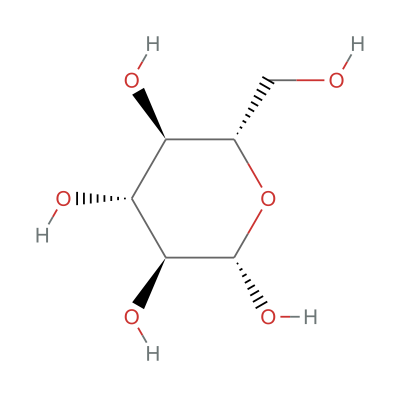

```mathematica
MoleculePlot[Entity["Chemical","DPlusGlucose"]]
```

Many molecules, especially hydrocarbons, undergo reactions called “polymerization”. A polymerization reaction is when individual monomers combine to form a polymer.

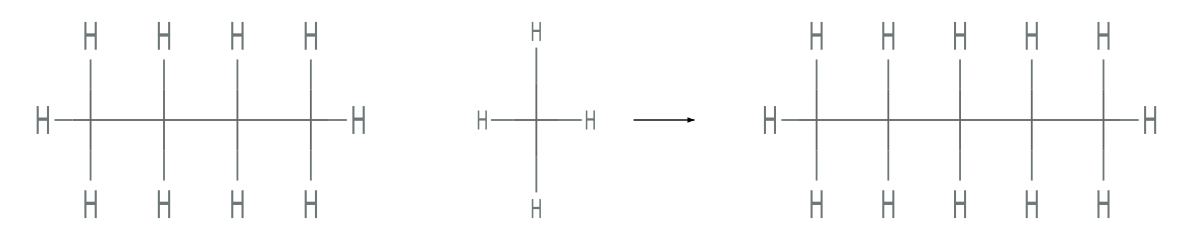

```mathematica
GraphicsRow[{MoleculePlot["Butane", IncludeHydrogens -> True],Style["+",FontSize->Large],MoleculePlot["Methane"],Graphics[{Arrowheads[Medium],Arrow[{{0,0},{1,0}}]}],MoleculePlot["Pentane", IncludeHydrogens -> True]}]
```

In this reaction, a 4-carbon polymer called butane reacts with a 1-carbon polymer called methane to create a 5-carbon polymer called pentane.

This can be modeled by a rule, where each time the rule is is applied to a graph it corresponds to a methane molecule being added to the end of a polymer.
Such a rule would look like this:

{{1,2},{1,3},{1,4},{1,5},{1,1}}->{{1,2},{1,3},{1,4},{1,5},{5,5},{5,6},{5,7},{5,8},{5,9}}

## Hello from Hausdorff

Some of our graphs, especially in 2 dimensions, seem to get very dense, especially after the simulation has been running for hundreds or thousands of steps. When we render them in 3 dimensions, they don’t seem to have this problem (or if they do it begins later).

It almost looks like the graph “doesn’t fit” in 2-dimensional (or 3-dimensional) space. Perhaps there is some measure of the dimension of the graph that we can use to justify this?

### Hausdorff Dimension

The problem happens once the Hausdorff dimension of the graph becomes higher than that of the space it is embedded in.

To calculate a Hausdorff dimension, we can find the adjacency matrix (or tensor) for a hypergraph. The principal eigenvalue will then be the hausdorff dimension of the graph.

```mathematica
getHausdorff[connections_]:=DecimalForm/@Eigenvalues[AdjacencyMatrix[Graph[connections]]]
```

## Future Work

Define point positions & velocities with differential equations and use a more efficient method to solve, for example Runge-Kutta (the current method for calculating positions and velocities is equivalent to Euler’s method)

Would greatly speed up processing time to generate animation

Parallelize rendering process across multiple kernels

Model large groups of vertices as “chunks” that exert a singular electric force to keep forces at large scales accurate while reducing computation time.

## Citations

Sauras-Altuzarra, Lorenzo and Weisstein, Eric W. “Adjacency Matrix.” From MathWorld--A Wolfram Web Resource. https://mathworld.wolfram.com/AdjacencyMatrix.html

Animating Wolfram Model evolutions in 3D​
by Dugan Hammock​
Wolfram Community, STAFF PICKS, July 12, 2023
​https://community.wolfram.com/groups/-/m/t/2959098

Wolfram Physics Project (2020), “Registry of Notable Universes”, 
https://www.wolframphysics.org/universes/

Maximillian Niederman the goat

## Acknowledgements

Thank you to my mentor Dugan Hammock for providing me with a basis upon which to build this project, to Jason Sonnenberg for helping with the chemistry aspect, and to Maximillian Niederman for the tag system code.